Basic setup

```mathematica
Quiet[Needs["QDENSITY`Qdensity`"]];
Quiet[Needs["QDENSITY`QCWave`"]];
?QDENSITY`Qdensity`*
```

General useful definitions such as gates etc.

```mathematica
KP[r__]:=KroneckerProduct[r]
StyleNumber[number_] :=Style[number,Bold,Darker[Green]]
Stokesfromρ[ρ_]:=(t =Table[Re[Tr[Subscript[σ, i].ρ]],{i,1,3}]//N; t)
StokesfromρStyled[ρ_]:=(t =Table[If[Abs[Re[Tr[Subscript[σ, i].ρ]]]>0.4,StyleNumber[Re[Tr[Subscript[σ, i].ρ]]],Re[Tr[Subscript[σ, i].ρ]]],{i,1,3}]//N; t)
ρfromψ[ψ_] :=ψ.ψ†;
Stokesfromψ[ψ_]:=Stokesfromρ[ρfromψ[ψ]];
Fidfromρ[ρ_,σ_]:=Re[Tr[MatrixPower[MatrixPower[ρ,0.5].σ.MatrixPower[ρ,0.5],0.5]]^2];
MixedState=𝕀/2;(*Mixed state*)
transformAndNorm[state_,U_]:=(out=U.state.U†;out=out/Tr[out]);
norm[state_]:=state/Tr[state];
transform[state_,U_]:=U.state.U†;

measureOut[state_]:=KP[Subscript[𝒫, 0],Subscript[σ, 0]].state.KP[Subscript[𝒫, 0],Subscript[σ, 0]]†+KP[Subscript[𝒫, 1],Subscript[σ, 0]].state.KP[Subscript[𝒫, 1],Subscript[σ, 0]]†;
measureOutAndBranch[state_,U0_,U1_]:=U0.KP[Subscript[𝒫, 0],Subscript[σ, 0]].state.KP[Subscript[𝒫, 0],Subscript[σ, 0]]†.U0†+U1.KP[Subscript[𝒫, 1],Subscript[σ, 0]].state.KP[Subscript[𝒫, 1],Subscript[σ, 0]]†.U1†;
```

```mathematica
(*Single qubit gates*)
{rxp,rXp,ryp,rYp,rzp,rZp}=Table[AF[MatrixExp[-ⅈ*Subscript[σ, Floor[j/2-0.01]+1]*π/(2*(1+Mod[j,2]))]],{j,1,6}];
{rxm,rXm,rym,rYm,rzm,rZm}=Table[AF[MatrixExp[ⅈ*Subscript[σ, Floor[j/2-0.01]+1]*π/(2*(1+Mod[j,2]))]],{j,1,6}];
rThetaX[θ_]=MatrixExp[-ⅈ*Subscript[σ, 1]*θ/2];
rThetaY[θ_]=MatrixExp[-ⅈ*Subscript[σ, 2]*θ/2];
rThetaZ[θ_]=MatrixExp[-ⅈ*Subscript[σ, 3]*θ/2];
rThetaϕ[θ_,ϕ_]=MatrixExp[-ⅈ*(Cos[ϕ] Subscript[σ, 1]*θ+Sin[ϕ] Subscript[σ, 2]*θ)/2];
```

Our nuclear spin parameters for both setups:

```mathematica
(*LT3*)
ωL3 = 2*π*447747.11;
wL31=2*π*425341.4;
Aperp3 =2*π*(87.5)*10^3;
Apar3 = -2*π*(30.0)*10^3 ;
par3 = ωL3+Apar3;
LT3WrongRotate =  True;

(*LT4*)
ωL4 = 2π 443172.12;
ωL41=2π 416572.34;
Aperp4 =2*π*(35.0)*10^3;
Apar4 =-2*π*(33.0)*10^3 ; (*because we use the -1 transition here*)
par4=Apar4+ωL4;

(*carbon parameters as a list*)
LT3C = {ωL3,par3-545.2,Aperp3};
LT3C[[3]]=Sqrt[(wL31 )^2-LT3C[[2]]^2]; (*Gate parameters have to be slightly adjusted*)

LT4C={ωL4,par4+34349.1,1};
LT4C[[3]]=Sqrt[(ωL41)^2-LT4C[[2]]^2]; (*Gate parameters have to be slightly adjusted*)
```

The system Hamiltonian with NV and Carbon reads

```mathematica
Usys[t_,{ω_,par_,Aperp_}] := MatrixExp[-ⅈ t/2(ω KP[Subscript[𝒫, 0],Subscript[σ, 3]]+KP[Subscript[𝒫, 1],(par Subscript[σ, 3]+Aperp*Subscript[σ, 1])])];
```

Import the pulse sequences

```mathematica
getPulses[basedir_,measname_]:=Module[{filename,x,attrs,seqOverview,PulseSeqs},
filename=If[FileExtension["filename"]=="",measname<>".h5",measname];
seqOverview={};
attrs={"seq_overview/name","seq_overview/trigger_wait","seq_overview/goto_target","seq_overview/jump_target","seq_overview/final_time"};
For[x=1,x≤Dimensions[attrs][[1]],x++,AppendTo[seqOverview,Import[basedir<>filename,{"Datasets",attrs[[x]]}]]];
seqOverview=Transpose[seqOverview];
PulseSeqs={};
For[x=0,x<Dimensions[seqOverview][[1]],x++,AppendTo[PulseSeqs,Import[basedir<>filename,{"Datasets","pulses/"<>ToString[x]}]]];
seqOverview=Transpose[seqOverview];
Transpose[{Transpose[seqOverview],PulseSeqs}]]
```

```mathematica
basedirLT4 = "/Users/humphreys/Repositories/personal_calcs/Work/Modelling/PulseSim/LT4/";
basedirLT3 = "/Users/humphreys/Repositories/personal_calcs/Work/Modelling/PulseSim/LT3/";
basedirLT3w = "/Users/humphreys/Repositories/personal_calcs/Work/Modelling/PulseSim/LT3w/";
```

Compiler!

Each pulse has a few params:
1.) Centre of pulse
2.) Pulse duration (less useful here)
3.) Phase angle of pulse - for some reason, in the compiled sequences, 0 encodes Y gate, π/2 encodes X gate, 3 π/2 encodes - X gate, π encodes - Y gate
4.) The rotation angle (basically pi/2 or pi)
5.) Special. 1 is repump, 2 is readout (readout is not implemented in all of the datasets, but is also not necessary)

The pulse seq also has some extra data, like what it jumps to, and most importantly, the total length of the pulse sequence.

```mathematica
compiledPulse[{ω_,Apar_,Aperp_},pulseData_,RotateOtherWay_:False,ignoreFinal_:False,triggerReadout_:False,readoutVal_:0]:=Module[{i,numPulses,evMat,pulseMat,pulseDelay,compiledPulse},
numPulses=Dimensions[pulseData[[2]]][[1]];
compiledPulse=IdentityMatrix[4];
For[i=1,i<=numPulses,i++,
pulseDelay=If[i==1, pulseData[[2,i,1]],(pulseData[[2,i,1]]-pulseData[[2,i-1,1]])];
evMat=Usys[pulseDelay,{ω,Apar,Aperp}];
pulseMat=Which[pulseData[[2,i,5]]==0,KP[rThetaϕ[pulseData[[2,i,4]],If[RotateOtherWay,-1,1]( π/2-pulseData[[2,i,3]])],Subscript[σ, 0]],pulseData[[2,i,5]]==1,KP[Subscript[𝒫, 0],Subscript[σ, 0]],pulseData[[2,i,5]]==2,If[triggerReadout,KP[Subscript[𝒫, readoutVal],Subscript[σ, 0]],KP[Subscript[σ, 0],Subscript[σ, 0]]]];
compiledPulse=pulseMat.evMat.compiledPulse;
];
pulseDelay=If[Not[ignoreFinal],(pulseData[[1,5]]-pulseData[[2,-1,1]]),0];
compiledPulse=Usys[pulseDelay,{ω,Apar,Aperp}].compiledPulse;
Return[compiledPulse]
]
```

I just wrote this, it tries to keep track of the phase during a pulse sequence (for human readability)

```mathematica
URot[t_,{ω_,par_,Aperp_},eState_] := MatrixExp[-ⅈ t/2(ω Tr[Subscript[𝒫, 0].eState] Subscript[σ, 3]+Sqrt[par^2 +Aperp^2]Tr[Subscript[𝒫, 1].eState] Subscript[σ, 3])];
```

```mathematica
Clear[compiledRotMat]
```

```mathematica
compiledRotMat[{ω_,Apar_,Aperp_},pulseData_,inputEState_,refState_:Subscript[σ, 0]/2,ignoreFinal_:False,triggerReadout_:False,readoutVal_:0]:=Module[{i,numPulses,evMat,eState,refRotMat,pulseMat,pulseDelay,compiledPulse},
numPulses=Dimensions[pulseData[[2]]][[1]];
compiledPulse=IdentityMatrix[2];

eState=inputEState;
For[i=1,i<=numPulses,i++,
pulseDelay=If[i==1, pulseData[[2,i,1]],(pulseData[[2,i,1]]-pulseData[[2,i-1,1]])];
evMat=URot[pulseDelay,{ω,Apar,Aperp},eState];
compiledPulse=evMat.compiledPulse;

pulseMat=Which[pulseData[[2,i,5]]==0,rThetaϕ[pulseData[[2,i,4]],(π/2-pulseData[[2,i,3]])],pulseData[[2,i,5]]==1,Subscript[𝒫, 0],pulseData[[2,i,5]]==2,If[triggerReadout,Subscript[𝒫, readoutVal],Subscript[σ, 0]]];
eState=pulseMat.eState.pulseMat†;

];
pulseDelay=If[Not[ignoreFinal],(pulseData[[1,5]]-pulseData[[2,-1,1]]),0];
compiledPulse=URot[pulseDelay,{ω,Apar,Aperp},eState].compiledPulse;

If[refState!=Subscript[σ, 0]/2,
refRotMat=rThetaZ[ArcTan[Re[Tr[Subscript[σ, 1].refState]],Re[Tr[Subscript[σ, 2].refState]]]];
compiledPulse=refRotMat.compiledPulse;];

Return[compiledPulse]
]
```

```mathematica
phaseEvolution[{ω_,Apar_,Aperp_},pulseData_,inputEstate_,inPhase_:0,ignoreFinal_:False,triggerReadout_:False,readoutVal_:0]:=Module[{i,numPulses,estate,PhaseTerm,finalPhaseTerm,pulseMat,pulseDelay,rotFact},
numPulses=Dimensions[pulseData[[2]]][[1]];
estate=inputEstate;

For[i=1,i<=numPulses,i++,
pulseDelay=If[i==1, pulseData[[2,i,1]],(pulseData[[2,i,1]]-pulseData[[2,i-1,1]])];
rotFact=Exp[-ⅈ pulseDelay/2(ω Abs[estate[[1,1]]]^2+Abs[estate[[2,1]]]^2Sqrt[Apar^2+Aperp^2])];
PhaseTerm=If[i==1,PhaseTerm={Exp[-ⅈ (π/180)inPhase ]rotFact},Append[PhaseTerm ,PhaseTerm [[-1]]rotFact]];

pulseMat=Which[pulseData[[2,i,5]]==0,rThetaϕ[pulseData[[2,i,4]],(π/2-pulseData[[2,i,3]])],pulseData[[2,i,5]]==1,Subscript[𝒫, 0],pulseData[[2,i,5]]==2,If[triggerReadout,Subscript[𝒫, readoutVal],Subscript[σ, 0]]];
estate=pulseMat.estate;

];
pulseDelay=If[Not[ignoreFinal],(pulseData[[1,5]]-pulseData[[2,-1,1]]),0];
rotFact=Exp[-ⅈ pulseDelay/2(ω Abs[estate[[1,1]]]^2+Abs[estate[[2,1]]]^2Sqrt[Apar^2+Aperp^2])];
finalPhaseTerm=PhaseTerm [[-1]]rotFact;
PhaseTerm=(180/π)Arg[PhaseTerm];
finalPhaseTerm=(180/π)Arg[finalPhaseTerm];
Return[{PhaseTerm,finalPhaseTerm}]
]

phaseEvolutionSimp[{ω_,Apar_,Aperp_},pulseData_,inputEstate_,ωsup_,inPhase_:0,ignoreFinal_:False,triggerReadout_:False,readoutVal_:0]:=Module[{i,numPulses,estate,currentEstate,PhaseTerm,finalPhaseTerm,pulseMat,pulseDelay,rotFact},
numPulses=Dimensions[pulseData[[2]]][[1]];
estate=inputEstate;
For[i=1,i<=numPulses,i++,
pulseDelay=If[i==1, pulseData[[2,i,1]],(pulseData[[2,i,1]]-pulseData[[2,i-1,1]])];

currentEstate=Which[Abs[estate[[1,1]]]^2>0.9,0,Abs[estate[[1,1]]]^2<0.1,1,True,0.5];
rotFact=Which[currentEstate==0,Exp[-ⅈ pulseDelay/2(ω)],currentEstate==1,Exp[-ⅈ pulseDelay/2(Sqrt[Apar^2+Aperp^2])],currentEstate==0.5,Exp[-ⅈ pulseDelay/2(ωsup)]];
PhaseTerm=If[i==1,PhaseTerm={Exp[-ⅈ (π/180)inPhase ]rotFact},Append[PhaseTerm ,PhaseTerm [[-1]]rotFact]];

pulseMat=Which[pulseData[[2,i,5]]==0,rThetaϕ[pulseData[[2,i,4]],(π/2-pulseData[[2,i,3]])],pulseData[[2,i,5]]==1,Subscript[𝒫, 0],pulseData[[2,i,5]]==2,If[triggerReadout,Subscript[𝒫, readoutVal],Subscript[σ, 0]]];
estate=pulseMat.estate;

];
pulseDelay=If[Not[ignoreFinal],(pulseData[[1,5]]-pulseData[[2,-1,1]]),0];

currentEstate=Which[Abs[estate[[1,1]]]^2>0.9,0,Abs[estate[[1,1]]]^2<0.1,1,True,0.5];
rotFact=Which[currentEstate==0,Exp[-ⅈ pulseDelay/2(ω)],currentEstate==1,Exp[-ⅈ pulseDelay/2(Sqrt[Apar^2+Aperp^2])],currentEstate==0.5,Exp[-ⅈ pulseDelay/2(ωsup)]];
finalPhaseTerm=PhaseTerm [[-1]]rotFact;

PhaseTerm=(180/π)Arg[PhaseTerm];
finalPhaseTerm=(180/π)Arg[finalPhaseTerm];

Return[{PhaseTerm,finalPhaseTerm}]
]
```

```mathematica
addPhaseEvInfo[CarbonParams_,pulseData_,inputEstate_,ωsup_,inPhase_:0]:=
Join[pulseData[[2]],Transpose[{phaseEvolutionSimp[CarbonParams,pulseData,inputEstate,ωsup,inPhase][[1]]}],2];
```

Carbon calib

### LT4

```mathematica
LT4phase=getPulses[basedirLT4,"AWG_seqs_phase_C4"];
```

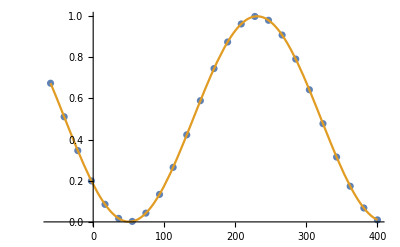

129.55

```mathematica
numPoints =Dimensions[LT4phase][[1]]/3;
phase=-60+Range[0,numPoints-1]*(460./(numPoints-1));
MeasVals={};
For[i=1,i≤numPoints,i++,
InitLT4=KP[Subscript[𝒫, 0],Subscript[σ, 0]].compiledPulse[LT4C,LT4phase[[3(i-1)+2]]];
MeasLT4=compiledPulse[LT4C,LT4phase[[3(i-1)+3]]];
pulse=MeasLT4.InitLT4;
initState=KP[Subscript[𝒫, 0],Subscript[σ, 0]/2];
outState=PTr[{2},transformAndNorm[initState,pulse]];
MeasVals=Append[MeasVals,Tr[Subscript[𝒫, 0].outState]];]
Clear[x];
nlmLT4=NonlinearModelFit[Transpose[{phase,MeasVals}],Amp*Cos[2π (f x+a/360)]+off,{{f,1/360},{a,0},{Amp,1},{off,0.5}},x];
plot2 =Show[ListPlot[{Transpose[{phase,MeasVals}]},Joined->{False}],Plot[Normal[nlmLT4],{x,phase[[1]],phase[[-1]]},PlotStyle->{ColorData[97,"ColorList"][[2]]}]]
aout=If[Amp>0,Mod[a,360],Mod[a+180,360]]/.nlmLT4["BestFitParameters"]
```

#### Simulate the phase offset calibration

The only phase adding element is the trigger duration (plus 2 extra microseconds that are added on each side)

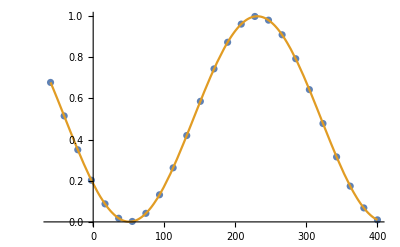

129.107

```mathematica
triggerRODuration=80*^-6;
phaseAfterTrig=Mod[(triggerRODuration+2*^-6)*ωL4,2π];
phaseToComp=Mod[2π-phaseAfterTrig,2π] ;
(* This is therefore the phase that needs to be 'added' to get back to zero.*)

InitLT4=compiledPulse[LT4C,LT4phase[[2]]];
initState=KP[Subscript[𝒫, 0],Subscript[σ, 0]/2];
ZProj=Table[{θ,Re@Tr[Subscript[𝒫, 0].PTr[{2},transformAndNorm[initState,InitLT4.Usys[Round[((phaseToComp+θ π/180) /ωL4)*1*^9]*1*^-9,LT4C].KP[Subscript[𝒫, 0],Subscript[σ, 0]].InitLT4]]]},{θ,phase}];
nlmLT4=NonlinearModelFit[ZProj,Amp*Cos[2π (f x+a/360)]+off,{{f,1/360},{a,0},{Amp,1},{off,0.5}},x];
plot2 =Show[ListPlot[ZProj,Joined->{False}],Plot[Normal[nlmLT4],{x,ZProj[[1,1]],ZProj[[-1,1]]},PlotStyle->{ColorData[97,"ColorList"][[2]]}]]
aout=If[Amp>0,Mod[a,360],Mod[a+180,360]]/.nlmLT4["BestFitParameters"]
```

### LT3

```mathematica
LT3phase=getPulses[basedirLT3,"AWG_seqs_phase_C1"];
```

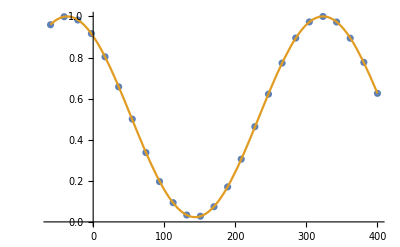

36.64

```mathematica
numPoints =Dimensions[LT3phase][[1]]/3;
phase=-60+Range[0,numPoints-1]*(460./(numPoints-1));
MeasVals={};
Clear[i]
For[i=1,i≤numPoints,i++,
InitLT3=KP[Subscript[𝒫, 0],Subscript[σ, 0]].compiledPulse[LT3C,LT3phase[[3(i-1)+2]],LT3WrongRotate];
MeasLT3=compiledPulse[LT3C,LT3phase[[3(i-1)+3]],LT3WrongRotate];
pulse=MeasLT3.InitLT3;
initState=KP[Subscript[𝒫, 0],Subscript[σ, 0]/2];
outState=PTr[{2},transformAndNorm[initState,pulse]];
MeasVals=Append[MeasVals,Tr[Subscript[𝒫, 0].outState]];]
Clear[x];
nlmLT3=NonlinearModelFit[Transpose[{phase,MeasVals}],Amp*Cos[2π (f x+a/360)]+off,{{f,1/360},{a,0},{Amp,1},{off,0.5}},x];
plot2 =Show[ListPlot[{Transpose[{phase,MeasVals}]},Joined->{False},PlotRange->{Automatic,{0,1}}],Plot[Normal[nlmLT3],{x,phase[[1]],phase[[-1]]},PlotStyle->{ColorData[97,"ColorList"][[2]]}]]
aout=If[Amp>0,Mod[a,360],Mod[a+180,360]]/.nlmLT3["BestFitParameters"]
```

#### Simulate the phase offset calibration

The only phase adding element is the trigger duration (plus 2 extra microseconds that are added on each side)

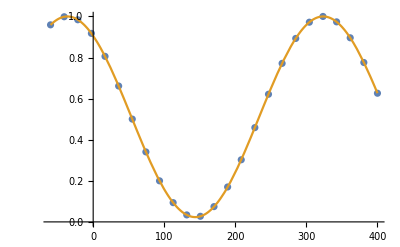

36.3029

```mathematica
triggerRODuration=90*^-6;
phaseAfterTrig=Mod[(triggerRODuration+2*^-6)*ωL3,2π];
phaseToComp=Mod[2π-phaseAfterTrig,2π] ;
(* This is therefore the phase that needs to be 'added' to get back to zero.*)

InitLT3=compiledPulse[LT3C,LT3phase[[2]],LT3WrongRotate];
initState=KP[Subscript[𝒫, 0],Subscript[σ, 0]/2];
ZProj=Table[{θ,Re@Tr[Subscript[𝒫, 0].PTr[{2},transformAndNorm[initState,InitLT3.Usys[Round[((phaseToComp+θ π/180) /ωL3)*1*^9]*1*^-9,LT3C].KP[Subscript[𝒫, 0],Subscript[σ, 0]].InitLT3]]]},{θ,phase}];
nlmLT3=NonlinearModelFit[ZProj,Amp*Cos[2π (f x+a/360)]+off,{{f,1/360},{a,0},{Amp,1},{off,0.5}},x];
plot2 =Show[ListPlot[ZProj,Joined->{False}],Plot[Normal[nlmLT3],{x,ZProj[[1,1]],ZProj[[-1,1]]},PlotStyle->{ColorData[97,"ColorList"][[2]]}]]
aout=If[Amp>0,Mod[a,360],Mod[a+180,360]]/.nlmLT3["BestFitParameters"]
```

Init methods

### MBI

```mathematica
MBI=getPulses[basedirLT4,"AWG_seqs_MBI"];
```

```mathematica
MBI[[;;,1]]
```

(MBI_0 | 1 | MBI_0 | C_MBI1_C4_y_pt0_tau_0_N_0 | 0.000029756
C_MBI1_C4_y_pt0_tau_0_N_0 | 1 | MBI_0 | Tomo_y_pi2_init0_tau_0_N_0 | 0.000517608
Tomo_y_pi2_init0_tau_0_N_0 | 0 | MBI_1 | C_MBI1_C4_y_pt1_tau_0_N_0 | 0.000478044
MBI_1 | 1 | MBI_1 | C_MBI1_C4_y_pt1_tau_0_N_0 | 0.000478044
C_MBI1_C4_y_pt1_tau_0_N_0 | 1 | MBI_1 | Tomo_y_pi2_init1_tau_0_N_0 | 0.000517608
Tomo_y_pi2_init1_tau_0_N_0 | 0 | MBI_2 | C_MBI1_C4_y_pt2_tau_0_N_0 | 0.00047748
MBI_2 | 1 | MBI_2 | C_MBI1_C4_y_pt2_tau_0_N_0 | 0.00047748
C_MBI1_C4_y_pt2_tau_0_N_0 | 1 | MBI_2 | phase_gate_Tomo4_Ren_a_24_2_tau_0_N_0 | 0.000517608
phase_gate_Tomo4_Ren_a_24_2_tau_0_N_0 | 0 | None | None | 0.000885228)

```mathematica
MBIinit=KP[Subscript[𝒫, 0],Subscript[σ, 0]].compiledPulse[LT4C,MBI[[2]]];

TomoLT4MBIX=compiledPulse[LT4C,MBI[[3]]];
TomoLT4MBIY=compiledPulse[LT4C,MBI[[6]]];
TomoLT4MBIZ=compiledPulse[LT4C,MBI[[9]]];

TomoMBI={TomoLT4MBIX,TomoLT4MBIY,TomoLT4MBIZ};
```

Init sets the carbon to something along the equator

```mathematica
pulseLT4=MBIinit;
initState=KP[Subscript[𝒫, 0],Subscript[σ, 0]/2];

outState=PTr[{1},transformAndNorm[initState,pulseLT4]]

MBIrot=compiledRotMat[LT4C,MBI[[2]],ρfromψ[Ket[0]]];
refX=MBIrot†.outState.MBIrot;

MBIrot=compiledRotMat[LT4C,MBI[[2]],ρfromψ[Ket[0]],refX];
outStateNFrame=MBIrot†.outState.MBIrot
```

(0.489139+0. ⅈ | 0.443374-0.23045 ⅈ
0.443374+0.23045 ⅈ | 0.510861+0. ⅈ)

(0.489139+1.38778×10^-17 ⅈ | 0.499688-8.32667×10^-17 ⅈ
0.499688+8.32667×10^-17 ⅈ | 0.510861+0. ⅈ)

How does it look in different bases?

```mathematica
bases={"X","Y","Z"};
For[i=1,i≤3,i++,
pulseLT4=TomoMBI[[i]].MBIinit;
initState=KP[Subscript[𝒫, 0],Subscript[σ, 0]/2];
outState=PTr[{2},transformAndNorm[initState,pulseLT4]];
Print[bases[[i]]<>" "<>ToString[Re[Tr[Subscript[σ, 3].outState]]]]]
```

X 0.999226

Y 0.00155502

Z -0.120371

Well that seems to work!

### Swap

```mathematica
swapInit=getPulses[basedirLT4,"AWG_seqs_swap"];
```

```mathematica
swapInit[[;;,1]]
```

(MBI_0 | 1 | MBI_0 | C_swap1_C4_y_pt0_tau_0_N_0 | 0.000029756
C_swap1_C4_y_pt0_tau_0_N_0 | 1 | MBI_0 | Tomo_y_pi2_init0_tau_0_N_0 | 0.000967248
Tomo_y_pi2_init0_tau_0_N_0 | 0 | MBI_1 | C_swap1_C4_y_pt1_tau_0_N_0 | 0.00047948
MBI_1 | 1 | MBI_1 | C_swap1_C4_y_pt1_tau_0_N_0 | 0.00047948
C_swap1_C4_y_pt1_tau_0_N_0 | 1 | MBI_1 | Tomo_y_pi2_init1_tau_0_N_0 | 0.000967248
Tomo_y_pi2_init1_tau_0_N_0 | 0 | MBI_2 | C_swap1_C4_y_pt2_tau_0_N_0 | 0.000478916
MBI_2 | 1 | MBI_2 | C_swap1_C4_y_pt2_tau_0_N_0 | 0.000478916
C_swap1_C4_y_pt2_tau_0_N_0 | 1 | MBI_2 | phase_gate_Tomo4_Ren_a_25_2_tau_0_N_0 | 0.000967248
phase_gate_Tomo4_Ren_a_25_2_tau_0_N_0 | 0 | None | None | 0.000885228)

```mathematica
swapinit=KP[Subscript[𝒫, 0],Subscript[σ, 0]].compiledPulse[LT4C,swapInit[[2]]];

TomoLT4swapX=compiledPulse[LT4C,swapInit[[3]]];
TomoLT4swapY=compiledPulse[LT4C,swapInit[[6]]];
TomoLT4swapZ=compiledPulse[LT4C,swapInit[[9]]];

TomoSwap={TomoLT4swapX,TomoLT4swapY,TomoLT4swapZ};
```

Init sets the carbon to Z

```mathematica
pulseLT4=swapinit;
initState=KP[Subscript[𝒫, 0],Subscript[σ, 0]/2];
outState=PTr[{1},transformAndNorm[initState,pulseLT4]]
```

(0.998532+0. ⅈ | 0.0351821+0.00585294 ⅈ
0.0351821-0.00585294 ⅈ | 0.00146845+0. ⅈ)

How does it look in different bases?

```mathematica
bases={"X","Y","Z"};
For[i=1,i≤3,i++,
pulseLT4=TomoSwap[[i]].swapinit;
initState=KP[Subscript[𝒫, 0],Subscript[σ, 0]/2];
outState=PTr[{2},transformAndNorm[initState,pulseLT4]];
Print[bases[[i]]<>" "<>ToString[Re[Tr[Subscript[σ, 3].outState]]]]]
```

X -0.0910959

Y -0.0365607

Z 0.986593

That also seems to work!

### MBI y

```mathematica
MBIy=getPulses[basedirLT4,"AWG_seqs_MBI_y"];
```

```mathematica
MBI[[2,2]]==MBIy[[2,2]]
MBI[[2,1,5]]==MBIy[[2,1,5]]

MBI[[3,2]]==MBIy[[3,2]]
MBI[[3,1,5]]==MBIy[[3,1,5]]
```

True

True

False

False

```mathematica
MBIy[[;;,1]]
```

(MBI_0 | 1 | MBI_0 | C_MBI_y1_C4_y_pt0_tau_0_N_0 | 0.000029756
C_MBI_y1_C4_y_pt0_tau_0_N_0 | 1 | MBI_0 | Tomo_y_pi2_init0_tau_0_N_0 | 0.000517608
Tomo_y_pi2_init0_tau_0_N_0 | 0 | MBI_1 | C_MBI_y1_C4_y_pt1_tau_0_N_0 | 0.000478608
MBI_1 | 1 | MBI_1 | C_MBI_y1_C4_y_pt1_tau_0_N_0 | 0.000478608
C_MBI_y1_C4_y_pt1_tau_0_N_0 | 1 | MBI_1 | Tomo_y_pi2_init1_tau_0_N_0 | 0.000517608
Tomo_y_pi2_init1_tau_0_N_0 | 0 | MBI_2 | C_MBI_y1_C4_y_pt2_tau_0_N_0 | 0.000478044
MBI_2 | 1 | MBI_2 | C_MBI_y1_C4_y_pt2_tau_0_N_0 | 0.000478044
C_MBI_y1_C4_y_pt2_tau_0_N_0 | 1 | MBI_2 | phase_gate_Tomo4_Ren_a_24_2_tau_0_N_0 | 0.000517608
phase_gate_Tomo4_Ren_a_24_2_tau_0_N_0 | 0 | None | None | 0.000885228)

```mathematica
MBIinit=KP[Subscript[𝒫, 0],Subscript[σ, 0]].compiledPulse[LT4C,MBIy[[2]]];

TomoLT4MBIX=compiledPulse[LT4C,MBIy[[3]]];
TomoLT4MBIY=compiledPulse[LT4C,MBIy[[6]]];
TomoLT4MBIZ=compiledPulse[LT4C,MBIy[[9]]];

TomoMBI={TomoLT4MBIX,TomoLT4MBIY,TomoLT4MBIZ};
```

Init sets the carbon to something along the equator

```mathematica
pulseLT4=MBIinit;
initState=KP[Subscript[𝒫, 0],Subscript[σ, 0]/2];
outState=PTr[{1},transformAndNorm[initState,pulseLT4]]
```

(0.489139+0. ⅈ | 0.443374-0.23045 ⅈ
0.443374+0.23045 ⅈ | 0.510861+0. ⅈ)

How does it look in different bases?

```mathematica
bases={"X","Y","Z"};
For[i=1,i≤3,i++,
pulseLT4=TomoMBI[[i]].MBIinit;
initState=KP[Subscript[𝒫, 0],Subscript[σ, 0]/2];
outState=PTr[{2},transformAndNorm[initState,pulseLT4]];
Print[bases[[i]]<>" "<>ToString[Re[Tr[Subscript[σ, 3].outState]]]]]
```

X 0.0000177902

Y 0.999226

Z -0.120371

That also seems to work...

Elec to carbon swap

### LT4

```mathematica
LT4SwapX=getPulses[basedirLT4,"AWG_seqs_elc_carb_swap_X"];
```

```mathematica
LT4SwapY=getPulses[basedirLT4,"AWG_seqs_elc_carb_swap_Y"];
```

```mathematica
LT4SwapZ=getPulses[basedirLT4,"AWG_seqs_elc_carb_swap_Z"];
```

Check that the pulses match in the different files (apart from where deliberately different):

```mathematica
For[z=1,z<=Dimensions[LT4SwapX][[1]],z++,If[LT4SwapX[[z,2]]!=LT4SwapZ[[z,2]],Print[z]]]
For[z=1,z<=Dimensions[LT4SwapX][[1]],z++,If[LT4SwapX[[z,2]]!=LT4SwapY[[z,2]],Print[z]]]

For[z=1,z<=Dimensions[LT4SwapX][[1]],z++,If[LT4SwapX[[z,1,5]]!=LT4SwapZ[[z,1,5]],Print[z]]]
For[z=1,z<=Dimensions[LT4SwapX][[1]],z++,If[LT4SwapX[[z,1,5]]!=LT4SwapY[[z,1,5]],Print[z]]]
```

3

7

11

3

7

11

3

7

11

```mathematica
LT4SwapX[[3,2]]==LT4SwapX[[7,2]]
LT4SwapX[[3,2]]==LT4SwapX[[11,2]]
```

True

True

Ok, setup the different bits of the sequence!

```mathematica
LT4SwapX[[;;,1]]
```

(MBI_0 | 1 | MBI_0 | init_C4_y_pt0_tau_0_N_0 | 0.000029756
init_C4_y_pt0_tau_0_N_0 | 1 | MBI_0 | init_E_y_pt0_tau_0_N_0 | 0.000967248
init_E_y_pt0_tau_0_N_0 | 0 | MBI_0 | Tomo_y_pi2_init0_tau_0_N_0 | 0.0009708
Tomo_y_pi2_init0_tau_0_N_0 | 0 | MBI_1 | init_C4_y_pt1_tau_0_N_0 | 0.000478044
MBI_1 | 1 | MBI_1 | init_C4_y_pt1_tau_0_N_0 | 0.000478044
init_C4_y_pt1_tau_0_N_0 | 1 | MBI_1 | init_E_y_pt1_tau_0_N_0 | 0.000967248
init_E_y_pt1_tau_0_N_0 | 0 | MBI_1 | Tomo_y_pi2_init1_tau_0_N_0 | 0.0009708
Tomo_y_pi2_init1_tau_0_N_0 | 0 | MBI_2 | init_C4_y_pt2_tau_0_N_0 | 0.00047748
MBI_2 | 1 | MBI_2 | init_C4_y_pt2_tau_0_N_0 | 0.00047748
init_C4_y_pt2_tau_0_N_0 | 1 | MBI_2 | init_E_y_pt2_tau_0_N_0 | 0.000967248
init_E_y_pt2_tau_0_N_0 | 0 | MBI_2 | phase_gate_Tomo4_Ren_a_211_2_tau_0_N_0 | 0.0009708
phase_gate_Tomo4_Ren_a_211_2_tau_0_N_0 | 0 | None | None | 0.000885228)

```mathematica
InitLT4Swap=KP[Subscript[𝒫, 0],Subscript[σ, 0]].compiledPulse[LT4C,LT4SwapX[[2]]];

InitEAndSwapLT4SwapX=KP[Subscript[𝒫, 0],Subscript[σ, 0]].compiledPulse[LT4C,LT4SwapX[[3]]];
InitEAndSwapLT4SwapY=KP[Subscript[𝒫, 0],Subscript[σ, 0]].compiledPulse[LT4C,LT4SwapY[[3]]];
InitEAndSwapLT4SwapZ=KP[Subscript[𝒫, 0],Subscript[σ, 0]].compiledPulse[LT4C,LT4SwapZ[[3]]];

InitSwap={InitEAndSwapLT4SwapX,InitEAndSwapLT4SwapY,InitEAndSwapLT4SwapZ};

TomoLT4XSwapX=compiledPulse[LT4C,LT4SwapX[[4]]];
TomoLT4XSwapY=compiledPulse[LT4C,LT4SwapX[[8]]];
TomoLT4XSwapZ=compiledPulse[LT4C,LT4SwapX[[12]]];

TomoSwap={TomoLT4XSwapX,TomoLT4XSwapY,TomoLT4XSwapZ};
```

```mathematica
(*addPhaseEvInfo[LT4C,LT4SwapX[[3]],Ket[0],ωsup4,156.66376790160004]*)
```

Init sets the carbon to Z

```mathematica
pulseLT4=InitLT4Swap;
initState=KP[Subscript[𝒫, 0],Subscript[σ, 0]/2];
outState=PTr[{1},transformAndNorm[initState,pulseLT4]]
```

(0.998532+0. ⅈ | 0.0351821+0.00585294 ⅈ
0.0351821-0.00585294 ⅈ | 0.00146845+0. ⅈ)

Swap sets the carbon to Z

```mathematica
bases={"X","Y","Z"};
initPulseSeqs={LT4SwapX[[3]],LT4SwapY[[3]],LT4SwapZ[[3]]};

For[j=1,j≤3,j++,Print["Input: "<>bases[[j]]];
pulseLT4=InitSwap[[j]].InitLT4Swap;
initState=KP[Subscript[𝒫, 0],Subscript[σ, 0]/2];
outState=PTr[{1},transformAndNorm[initState,pulseLT4]];
Print[outState//TableForm];

Print["C Frame"];
MBIrot=compiledRotMat[LT4C,initPulseSeqs[[j]],Subscript[𝒫, 0]];(*.compiledRotMat[LT4C,LT4SwapX[[2]],Subscript[𝒫, 0],refX];*)
Print[(180/π)Arg[MBIrot[[2,2]]*Exp[-ⅈ Arg[MBIrot[[1,1]]]]]];
outStateNFrame=Chop[MBIrot†.outState.MBIrot];
Print[outStateNFrame//TableForm];

]
```

Input: X

0.999257+0. ⅈ | 0.021374+0.0168875 ⅈ
0.021374-0.0168875 ⅈ | 0.000742697+0. ⅈ

C Frame

155.215

0.999257 | -0.0264846-0.00637172 ⅈ
-0.0264846+0.00637172 ⅈ | 0.000742697

Input: Y

0.475211+0. ⅈ | 0.226271+0.445182 ⅈ
0.226271-0.445182 ⅈ | 0.524789+0. ⅈ

C Frame

127.39

0.475211 | -0.491106-0.0905575 ⅈ
-0.491106+0.0905575 ⅈ | 0.524789

Input: Z

0.489667+0. ⅈ | 0.443381-0.230882 ⅈ
0.443381+0.230882 ⅈ | 0.510333+0. ⅈ

C Frame

168.215

0.489667 | -0.386882+0.316568 ⅈ
-0.386882-0.316568 ⅈ | 0.510333

```mathematica
pulseLT4=MBIinit;
initState=KP[Subscript[𝒫, 0],Subscript[σ, 0]/2];
outState=PTr[{1},transformAndNorm[initState,pulseLT4]]
```

(0.489139+0. ⅈ | 0.443374-0.23045 ⅈ
0.443374+0.23045 ⅈ | 0.510861+0. ⅈ)

How does it look in different tomo bases?

```mathematica
bases={"X","Y","Z"};
For[j=1,j≤3,j++,Print["Input: "<>bases[[j]]];For[i=1,i≤3,i++,
pulseLT4=TomoSwap[[i]].InitSwap[[j]].InitLT4Swap;
initState=KP[Subscript[𝒫, 0],Subscript[σ, 0]/2];
outState=PTr[{2},transformAndNorm[initState,pulseLT4]];
Print[bases[[i]]<>" "<>ToString[Re[Tr[Subscript[σ, 3].outState]]]]]]
```

Input: X

X 0.000918591

Y -0.0710881

Z 0.991544

Input: Y

X -0.00724499

Y -0.997057

Z -0.0366998

Input: Z

X 0.999613

Y 0.00229112

Z -0.11937

### LT3

```mathematica
LT3SwapX=getPulses[basedirLT3,"AWG_seqs_elc_carb_swap_X"];
```

```mathematica
LT3SwapY=getPulses[basedirLT3,"AWG_seqs_elc_carb_swap_Y"];
```

```mathematica
LT3SwapZ=getPulses[basedirLT3,"AWG_seqs_elc_carb_swap_Z"];
```

```mathematica
LT3SwapX[[;;,1]]
```

(MBI_0 | 1 | MBI_0 | init_C1_y_pt0_tau_0_N_0 | 0.00007936
init_C1_y_pt0_tau_0_N_0 | 1 | MBI_0 | init_E_y_pt0_tau_0_N_0 | 0.000614668
init_E_y_pt0_tau_0_N_0 | 0 | MBI_0 | Tomo_y_pi2_init0_tau_0_N_0 | 0.000617896
Tomo_y_pi2_init0_tau_0_N_0 | 0 | MBI_1 | init_C1_y_pt1_tau_0_N_0 | 0.0003542
MBI_1 | 1 | MBI_1 | init_C1_y_pt1_tau_0_N_0 | 0.0003542
init_C1_y_pt1_tau_0_N_0 | 1 | MBI_1 | init_E_y_pt1_tau_0_N_0 | 0.000614668
init_E_y_pt1_tau_0_N_0 | 0 | MBI_1 | Tomo_y_pi2_init1_tau_0_N_0 | 0.000617896
Tomo_y_pi2_init1_tau_0_N_0 | 0 | MBI_2 | init_C1_y_pt2_tau_0_N_0 | 0.000353644
MBI_2 | 1 | MBI_2 | init_C1_y_pt2_tau_0_N_0 | 0.000353644
init_C1_y_pt2_tau_0_N_0 | 1 | MBI_2 | init_E_y_pt2_tau_0_N_0 | 0.000614668
init_E_y_pt2_tau_0_N_0 | 0 | MBI_2 | phase_gate_Tomo1_Ren_a_211_2_tau_0_N_0 | 0.000617896
phase_gate_Tomo1_Ren_a_211_2_tau_0_N_0 | 0 | None | None | 0.00053486)

```mathematica
InitLT3Swap=KP[Subscript[𝒫, 0],Subscript[σ, 0]].compiledPulse[LT3C,LT3SwapX[[2]],LT3WrongRotate];

InitEAndSwapLT3SwapX=KP[Subscript[𝒫, 0],Subscript[σ, 0]].compiledPulse[LT3C,LT3SwapX[[3]],LT3WrongRotate];
InitEAndSwapLT3SwapY=KP[Subscript[𝒫, 0],Subscript[σ, 0]].compiledPulse[LT3C,LT3SwapY[[3]],LT3WrongRotate];
InitEAndSwapLT3SwapZ=KP[Subscript[𝒫, 0],Subscript[σ, 0]].compiledPulse[LT3C,LT3SwapZ[[3]],LT3WrongRotate];

InitSwap={InitEAndSwapLT3SwapX,InitEAndSwapLT3SwapY,InitEAndSwapLT3SwapZ};

TomoLT3XSwapX=compiledPulse[LT3C,LT3SwapX[[4]],LT3WrongRotate];
TomoLT3XSwapY=compiledPulse[LT3C,LT3SwapX[[8]],LT3WrongRotate];
TomoLT3XSwapZ=compiledPulse[LT3C,LT3SwapX[[12]],LT3WrongRotate];

TomoSwap={TomoLT3XSwapX,TomoLT3XSwapY,TomoLT3XSwapZ};

pulseLT3=InitLT3Swap;
initState=KP[Subscript[𝒫, 0],Subscript[σ, 0]/2];
outState=PTr[{1},transformAndNorm[initState,pulseLT3]]

bases={"X","Y","Z"};
For[j=1,j≤3,j++,Print["Input: "<>bases[[j]]];For[i=1,i≤3,i++,
pulseLT3=TomoSwap[[i]].InitSwap[[j]].InitLT3Swap;
initState=KP[Subscript[𝒫, 0],Subscript[σ, 0]/2];
outState=PTr[{2},transformAndNorm[initState,pulseLT3]];
Print[bases[[i]]<>" "<>ToString[Re[Tr[Subscript[σ, 3].outState]]]]]]
```

(0.00799484+0. ⅈ | 0.0514489-0.0723897 ⅈ
0.0514489+0.0723897 ⅈ | 0.992005+0. ⅈ)

Input: X

X -0.00458003

Y -0.152337

Z 0.960145

Input: Y

X -0.00107303

Y -0.987371

Z 0.155527

Input: Z

X 0.999909

Y 0.0275503

Z -0.23518